# Visibility of different interference measures

## Definitions

Here we define all the functions needed for our analysis

### Default Plot style

```mathematica
SetOptions[Plot, BaseStyle -> {FontFamily -> "cmr10", FontSize -> 20},
   Frame -> True, ImageSize -> 72*{8*GoldenRatio, 8}, 
  AspectRatio -> 1/GoldenRatio, LabelStyle -> Directive[Bold], 
  GridLines -> Automatic];
```

### Probabilities of different states

```mathematica
(*Coefficient of the wavefunction after the beam splitter in the Fock basis, Note that this is the most important defintion as all others rely upon it*)
Cf[Y_,X_,W_,Z_,λ_,ϕ_]:=(1-λ^2)*(λ/2)^(W+Y)*Sqrt[Factorial[Y]*Factorial[X]*Factorial[W]*Factorial[Z]]*Sum[1/(Factorial[m]*Factorial[W+Y-m])*Sum[Sum[I^(W+Z+2*m-2*k-2*n)*Exp[I*ϕ*(W+Z-2*m)]*Binomial[X+Z-m,W-k]*Binomial[m,k]*Binomial[W+Y-m,Z-n]*Binomial[m,n],{n,0,m}],{k,0,m}],{m,0,W+Y}]
(*Probability of a given (complete) four particle state, equal to cc^**)
Pst[Y_,W_,X_,λ_,ϕ_]:=Abs[Cf[Y,X,W,Y+W-X,λ,ϕ]]^2
(*Probability of a two particle state, tracing over the othe half*)
Pb[Y_,W_,λ_,ϕ_]:=Sum[Abs[Cf[Y,X,W,Y+W-X,λ,ϕ]]^2,{X,0,Y+W}]
(*Probability of seeing a given total number of particles*)
Pnum[Num_,λ_,ϕ_]:=Sum[Pb[Num-x,x,λ,ϕ],{x,0,Num}]
(*Probability of seeing a noncoincidence state*)
Pnc[λ_,ϕ_]:=Pb[0,0,λ,ϕ]+Sum[Pb[i,0,λ,ϕ]+Pb[0,i,λ,ϕ],{i,1,5}]
(*Calculates the visibility*)
Vis[a_,b_]:=1-Min[{a,b}]/Max[{a,b}];
```

### Expectation functions for g2's

```mathematica
(*Expectation of c- to order T*)
Ecm[λ_,ϕ_,T_]:=Sum[Sum[Pb[Y,W,λ,ϕ]*Y,{W,0,T}],{Y,0,T}]
(*Expectation of c+ to order T*)
Ecp[λ_,ϕ_,T_]:=Sum[Sum[Sum[Pst[Y,Z+X-Y,X,λ,ϕ]*X,{Y,0,Z+X}],{Z,0,T}],{X,0,T}]
(*Expectation of d-*)
Edm[λ_,ϕ_,T_]:=Sum[Sum[Pb[Y,W,λ,ϕ]*W,{Y,0,T}],{W,0,T}]
(*Expectation of d+ to order T*)
Edp[λ_,ϕ_,T_]:=Sum[Sum[Sum[Pst[Y,Z+X-Y,X,λ,ϕ]*Z,{Y,0,Z+X}],{X,0,T}],{Z,0,T}]
(*Expectation of cross product*)
Ecmdm[λ_,ϕ_,T_]:=Sum[Sum[Pb[Y,W,λ,ϕ]*W*Y,{Y,0,T}],{W,0,T}]
(**)
Ecpcm[λ_,ϕ_,T_]:=Sum[Sum[Sum[Pst[Y,W,X,λ,ϕ]*X*Y,{W,Max[X-Y,0],Max[X-Y,0]+T}],{Y,0,T}],{X,0,T}]
(**)
Ecpdp[λ_,ϕ_,T_]:=Sum[Sum[Sum[Pst[Y,Z+X-Y,X,λ,ϕ]*X*Z,{Y,0,Z+X}],{Z,0,T}],{X,0,T}]
(**)
Edpdm[λ_,ϕ_,T_]:=Sum[Sum[Sum[Pst[Y,W,Y+W-Z,λ,ϕ]*W*Z,{Y,Max[Z-W,0],Max[Z-W,0]+T}],{Z,0,T}],{W,0,T}]
(**)
Ecpdm[λ_,ϕ_,T_]:=Sum[Sum[Sum[Pst[Y,W,X,λ,ϕ]*W*X,{Y,Max[X-W,0],Max[X-W,0]+T}],{X,0,T}],{W,0,T}]
(**)
Edpcm[λ_,ϕ_,T_]:=Sum[Sum[Sum[Pst[Y,W,Y+W-Z,λ,ϕ]*Y*Z,{W,Max[Z-Y,0],Max[Z-Y,0]+T}],{Z,0,T}],{Y,0,T}]
```

### Distinguishable Case

```mathematica
(*Probability of no coincidence for distinguishable case*)
Pdnc[x_]:=(1-x)^2/(2-x)^2*(4+(4-x)*x)
(*Probability of N particle (actually pair) state, note that this probability is the smae for both the distinguishable and non-distinguishable cases*)
PN[N_,x_]:=x^N*(1-x)^2*(N+1)
```

## Basic Checks

A variety of basic checks to ensure that the definitions in the previous section are  likely correct (or at least not obviously wrong)

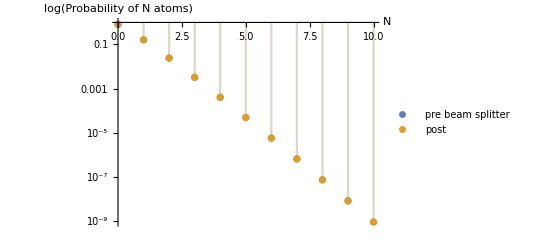

True

True

True

```mathematica
(*Check that the probability of finding a particular particle number remains the same before and after the beam splitter*)
n=0.1;(*mode occupancy*)
DiscretePlot[{PN[x,n],Pnum[x,Sqrt[n],1]},{x,0,10},ScalingFunctions->{None,"Log"},AxesLabel->{"N","log(Probability of N atoms)"},PlotLegends->{"pre beam splitter","post"}]
(*I caculated the first few terms of the expansion by hand and check those results against the definition above*)
Cf[0,0,0,0,λ,ϕ] ==(1-λ^2) (*the zeroth order*)
FullSimplify[Cf[1,0,0,1,λ,ϕ]]==FullSimplify[(1-λ^2)*λ*I*Cos[ϕ]](*a first order*)
FullSimplify[Cf[2,2,0,0,λ,ϕ]]==FullSimplify[(1-λ^2)/4*λ^2*(1+Exp[-4*I*ϕ]-2*Exp[-2*I*ϕ])](*and a second order*)
```

## Two port post selection

In this section we consider the case of only two ports (the equivalent of summing out one half of the Rarity-Tapster setup) and see if there is any useful measures to align/ anything of general interest

### Total number = 2

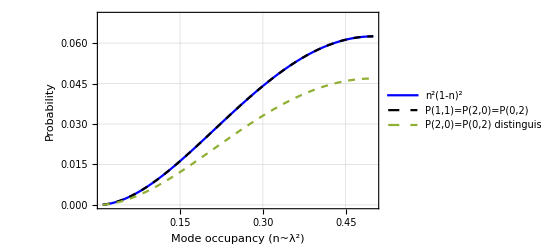

```mathematica
(*Probability of getting a given two particle state, note this probability is phase invariant*)
Plot[{1/3*PN[2,x] ,Pb[1, 1, Sqrt[x], Pi/2],1/4*PN[2,x]}, {x, 0.01, 0.5},FrameLabel-> {"Mode occupancy (n=λ^2)", "Probability"},PlotLegends -> {"n^2(1-n)^2", "P(1,1)=P(2,0)=P(0,2)","P(2,0)=P(0,2) distinguishable"},PlotStyle -> {Blue, {Dashed, Black},Dashed},PlotRange->{{0.01,0.5},{0,0.07}}]
```

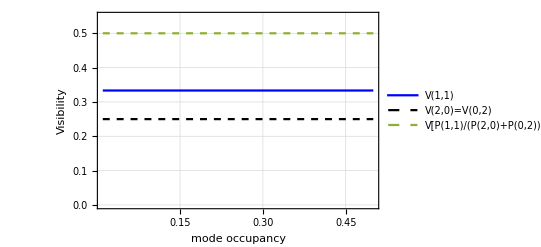

```mathematica
(*Visibiliy of the dips for the various states*)
Plot[{Vis[Pb[1,1,Sqrt[x],Pi/2],1/2*PN[2,x]],Vis[Pb[2,0,Sqrt[x],Pi/2],1/4*PN[2,x]],Vis[Pb[1,1,Sqrt[x],1]/(2*Pb[0,2,Sqrt[x],1]),1]},{x,0.01,0.5},FrameLabel -> {"Mode occupancy (n=λ^2)","Visibility"},PlotLegends -> {"V(1,1)", "V(2,0)=V(0,2)","V[P(1,1)/(P(2,0)+P(0,2))]"},PlotStyle -> {Blue, {Dashed, Black},Dashed},PlotRange->{{0.01,0.5},{0,0.55}}]
```

### Total number = 1

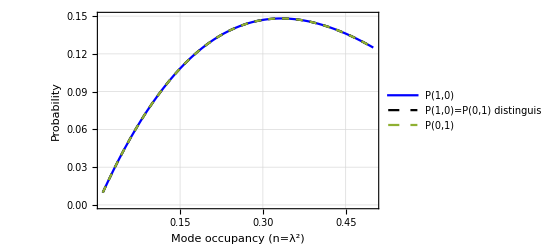

```mathematica
(*Probability of getting a given two particle state*)
Plot[{Pb[1, 0, Sqrt[x], Pi/2.4],1/2*PN[1,x],Pb[0, 1, Sqrt[x], Pi/2]}, {x, 0.01, 0.5},FrameLabel -> {"Mode occupancy (n=λ^2)","Probability"},PlotLegends -> { "P(1,0)","P(1,0)=P(0,1) distinguishable","P(0,1)"},PlotStyle -> {Blue, {Dashed, Black},Dashed},PlotRange->{{0.01,0.5},{0,0.15}}]
```

## Four port post selection

### Total pairs (particles) = 2 (4)

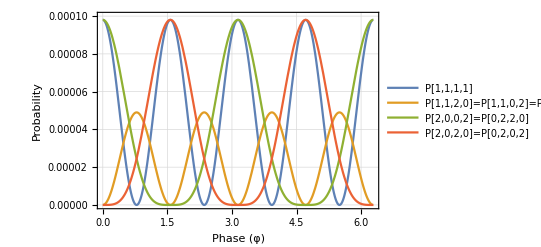

```mathematica
(*Probability against phase of all possible four port two pair states*)
Plot[{Pst[1,1,1,0.1,ϕ],Pst[1,1,2,0.1,ϕ],Pst[2,0,0,0.1,ϕ],Pst[2,0,2,0.1,ϕ]},{ϕ,0,2*Pi},PlotLegends->{"P[1,1,1,1]","P[1,1,2,0]=P[1,1,0,2]=P[0,2,1,1]=P[2,0,1,1]","P[2,0,0,2]=P[0,2,2,0]","P[2,0,2,0]=P[0,2,0,2]"},FrameLabel -> {"Phase (φ)", "Probability"},PlotRange->{{0,2*Pi},{0,0.0001}}]
```

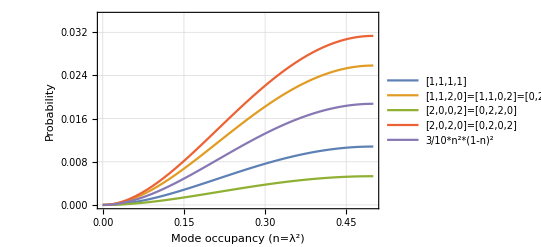

```mathematica
(*Probability of states against mode occupancy*)
Plot[{Pst[1,1,1,Sqrt[x],1],Pst[1,1,2,Sqrt[x],1],Pst[2,0,0,Sqrt[x],1],Pst[2,0,2,Sqrt[x],1],1/10*PN[2,x]},{x,0,0.5},PlotLegends->{"P[1,1,1,1]","P[1,1,2,0]=P[1,1,0,2]=P[0,2,1,1]=P[2,0,1,1]","P[2,0,0,2]=P[0,2,2,0]","P[2,0,2,0]=P[0,2,0,2]","3/10*n^2(1-n)^2"},FrameLabel -> {"Mode occupancy (n=λ^2)", "Probability"},PlotRange->{{0,0.5},{0,0.035}}]
```

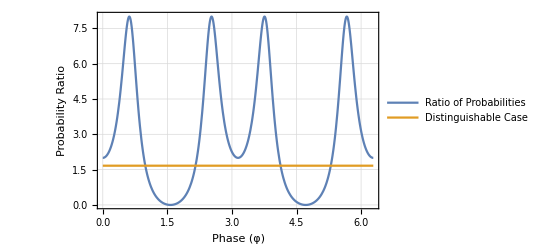

```mathematica
(*Ratio of states against phase*)
Plot[{(4*Pst[1,1,2,0.1,ϕ]+2*Pst[2,0,0,0.1,ϕ])/(Pst[1,1,1,0.1,ϕ]+2*Pst[2,0,2,0.1,ϕ]),5/3},{ϕ,0,2*Pi},PlotLegends->{"Ratio of Probabilities","Distinguishable Case"},FrameLabel -> {"Phase (φ)", "Probability Ratio"},PlotRange->{{0,2*Pi},{0,8.02}}]
```

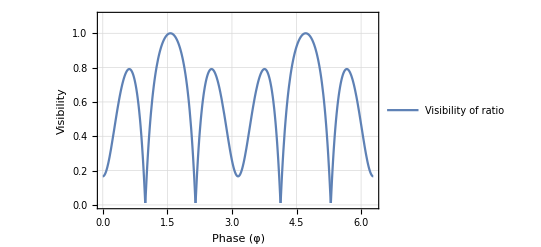

```mathematica
(*Visibility of ratio of states against phase*)
Plot[{Vis[(4*Pst[1,1,2,0.1,ϕ]+2*Pst[2,0,0,0.1,ϕ])/(Pst[1,1,1,0.1,ϕ]+2*Pst[2,0,2,0.1,ϕ]),5/3]},{ϕ,0,2*Pi},PlotLegends->{"Visibility of ratio"},FrameLabel -> {"Phase (φ)", "Visibility"},PlotRange->{{0,2*Pi},{0,1.1}}]
```

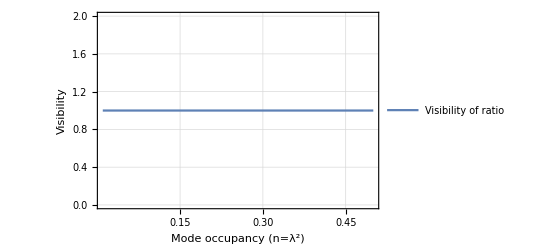

```mathematica
(*Visibility of ratio of states against mode occupancy for pi/2 phase*)
Plot[{Vis[(4*Pst[1,1,2,Sqrt[x],Pi/2]+2*Pst[2,0,0,Sqrt[x],Pi/2])/(Pst[1,1,1,Sqrt[x],Pi/2]+2*Pst[2,0,2,Sqrt[x],Pi/2]),5/3]},{x,0.01,0.5},PlotLegends->{"Visibility of ratio"},FrameLabel -> {"Mode occupancy (n=λ^2)", "Visibility"},PlotRange->{{0.01,0.5},{0,2.0}}]
```

### Total pairs (particles) = 1 (2)

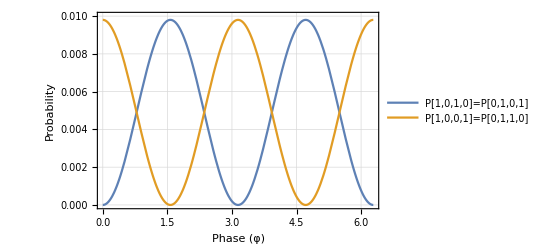

```mathematica
(*Probability against phase of all possible four port one pair states*)
Plot[{Pst[1,0,1,0.1,ϕ],Pst[1,0,0,0.1,ϕ]},{ϕ,0,2*Pi},PlotLegends->{"P[1,0,1,0]=P[0,1,0,1]","P[1,0,0,1]=P[0,1,1,0]"},FrameLabel -> {"Phase (φ)", "Probability"},PlotRange->{{0,2*Pi},{0,0.01}}]
```

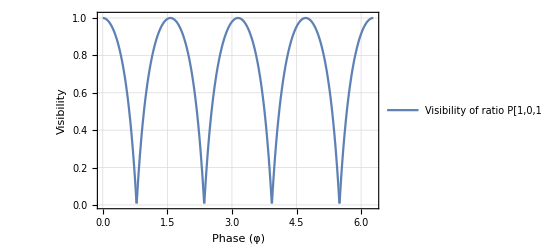

```mathematica
(*Visibility over phase of porbability ratio*)
Plot[{Vis[1,Pst[1,0,1,0.1,ϕ]/Pst[1,0,0,0.1,ϕ]]},{ϕ,0,2*Pi},PlotLegends->{"Visibility of ratio P[1,0,1,0]/P[1,0,0,1]"},FrameLabel -> {"Phase (φ)", "Visibility"},PlotRange->{{0,2*Pi},{0,1.01}}]
```

## Coincidence and Non-coincidence

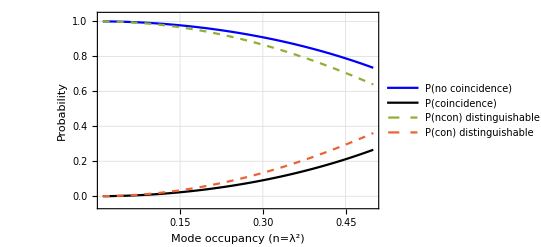

```mathematica
(*Comparison of coincidence and noncoicidence probabilities over mode occupancy for both (non)distinguisble*)
Plot[{Pnc[Sqrt[x],Pi/2],1-Pnc[Sqrt[x],Pi/2],Pdnc[x],1-Pdnc[x]},{x,0.01,0.5},FrameLabel->{"Mode occupancy (n=λ^2)","Probability"},PlotLegends->{"P(no coincidence)","P(coincidence)","P(ncon) distinguishable","P(con) distinguishable"},PlotStyle->{Blue,Black,Dashed,Dashed},PlotRange->{{0.01,0.5},{-0.05,1.03}}]
```

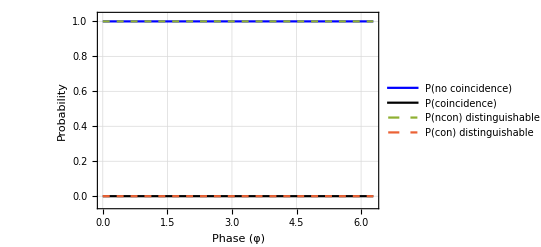

```mathematica
(*Comparison of coincidence and noncoicidence probabilities over phase for both (non)distinguisble*)
Plot[{Pnc[0.1,x],1-Pnc[0.1,x],Pdnc[0.01],1-Pdnc[0.01]},{x,0,2*Pi},FrameLabel->{"Phase (φ)", "Probability"},PlotLegends->{"P(no coincidence)","P(coincidence)","P(ncon) distinguishable","P(con) distinguishable"},PlotStyle->{Blue,Black,Dashed,Dashed},PlotRange->{{0,2*Pi},{-0.05,1.03}}]
```

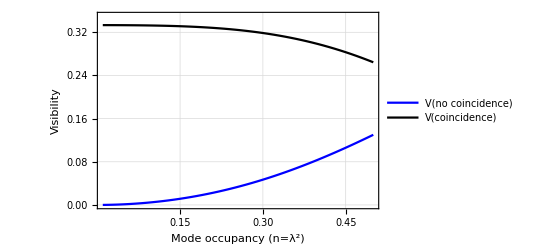

```mathematica
(*Visibility of coincidence and noncoicidence against mode occupancy*)
Plot[{Vis[ Pnc[Sqrt[x], Pi/2],Pdnc[x]],Vis[ 1 - Pnc[Sqrt[x], Pi/2],1 - Pdnc[x]]}, {x,0.01, 0.5},FrameLabel -> {"Mode occupancy (n=λ^2)","Visibility"},PlotLegends -> {"V(no coincidence)", "V(coincidence)"}, PlotStyle -> {Blue, Black},PlotRange->{{0.01,0.5},{0,0.35}}]
```

## Two port g^(2)

Next we consider the various possible two particle correlation functions (g^(2) for short) that can be constructed between the four ports of our Rarity-Tapster interferometer (3!=6 in total)

```mathematica
Ord=3 ;(*To what order in particle number we wish to calculate the g2's*)
```

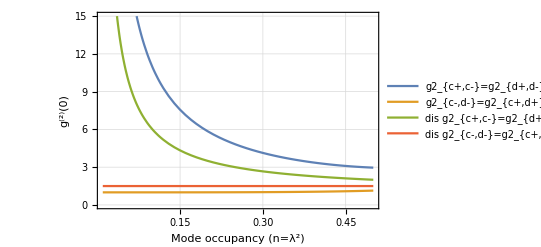

```mathematica
(*The six possible g2's along with their distinguishable counter parts*)
Plot[{Edpdm[Sqrt[x],Pi/2,Ord]/(Edm[Sqrt[x],Pi/2,Ord]*Edp[Sqrt[x],Pi/2,Ord]),Ecpdp[Sqrt[x],Pi/2,Ord]/(Edp[Sqrt[x],Pi/2,Ord]*Ecp[Sqrt[x],Pi/2,Ord]),1/(2*x)+1,3/2},{x,0.01,0.5},FrameLabel -> {"Mode occupancy (n=λ^2)","g^(2)(0)"},PlotLegends -> {"g2_{c+,c-}=g2_{d+,d-}","g2_{c-,d-}=g2_{c+,d+}=g2_{d+,c-}=g2_{c+,d-}","dis g2_{c+,c-}=g2_{d+,d-}=g2_{d+,c-}=g2_{c+,d-}","dis g2_{c-,d-}=g2_{c+,d+}"},PlotRange->{{0.01,0.5},{0,15}}]
```

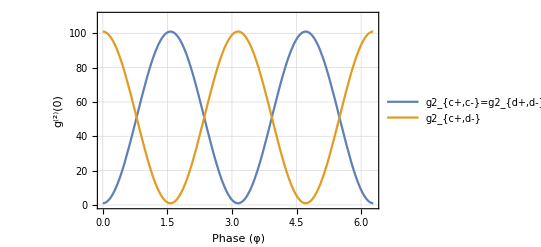

```mathematica
Plot[{Ecpcm[0.1,ϕ,Ord]/(Ecm[0.1,ϕ,Ord]*Ecp[0.1,ϕ,Ord]),Ecpdm[0.1,ϕ,Ord]/(Edm[0.1,ϕ,Ord]*Ecp[0.1,ϕ,Ord])},{ϕ,0,2*Pi},FrameLabel -> {"Phase (φ)","g^(2)(0)"},PlotLegends -> {"g2_{c+,c-}=g2_{d+,d-}","g2_{c+,d-}"},PlotRange->{{0,2*Pi},{0,110}}]
```

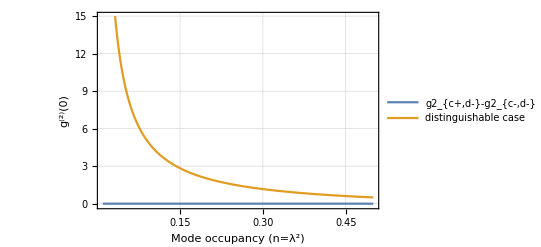

```mathematica
(*An interesting comparison*)
Plot[{Ecpdm[Sqrt[x],Pi/2,Ord]/(Edm[Sqrt[x],Pi/2,Ord]*Ecp[Sqrt[x],Pi/2,Ord])-Ecmdm[Sqrt[x],Pi/2,Ord]/(Edm[Sqrt[x],Pi/2,Ord]*Ecm[Sqrt[x],Pi/2,Ord]),1/(2*x)+1-3/2},{x,0.01,0.5},FrameLabel -> {"Mode occupancy (n=λ^2)","g^(2)(0)"},PlotLegends -> {"g2_{c+,d-}-g2_{c-,d-}","distinguishable case"},PlotRange->{{0.01,0.5},{-0.1,15}}]
```

## Four port g2

```mathematica
Ord=2 (*To what order in particle number we wish to calculate the g2's*)
```

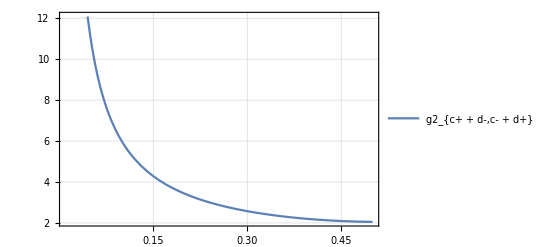

```mathematica
(*The six possible g2's*)
Plot[(Ecpcm[Sqrt[x],Pi/2,Ord]+Ecmdm[Sqrt[x],Pi/2,Ord]+Ecpdp[Sqrt[x],Pi/2,Ord]+Edpdm[Sqrt[x],Pi/2,Ord])/((Ecm[Sqrt[x],Pi/2,Ord]+Edp[Sqrt[x],Pi/2,Ord])*(Ecp[Sqrt[x],Pi/2,Ord]+Edm[Sqrt[x],Pi/2,Ord])),{x,0.01,0.5},FrameLabel -> {"Mode occupancy (n=λ^2)","g^(2)(0)"},PlotLegends -> {"g2_{c+ + d-,c- + d+}","g2_{d+,d-}","g2_{c+,d-}"},PlotRange->{{0.01,0.5},{0,12}}]
```

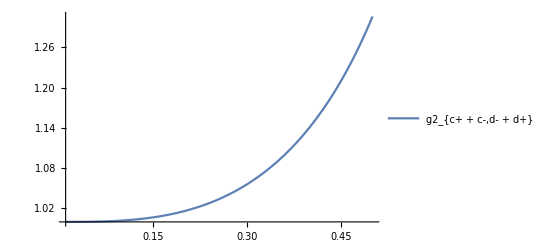

```mathematica
Plot[(Ecpdm[Sqrt[x],Pi/2,Ord]+Ecmdm[Sqrt[x],Pi/2,Ord]+Ecpdp[Sqrt[x],Pi/2,Ord]+Edpcm[Sqrt[x],Pi/2,Ord])/((Ecm[Sqrt[x],Pi/2,Ord]+Ecp[Sqrt[x],Pi/2,Ord])*(Edp[Sqrt[x],Pi/2,Ord]+Edm[Sqrt[x],Pi/2,Ord])),{x,0.01,0.5},PlotLegends -> {"g2_{c+ + c-,d- + d+}","g2_{d+,d-}"}]
```

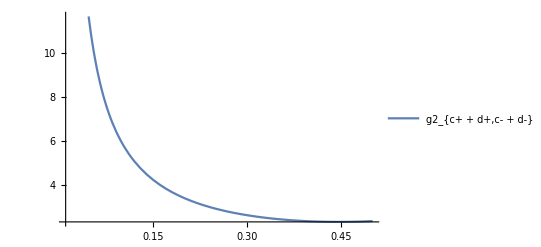

```mathematica
Plot[(Ecpdm[Sqrt[x],Pi/2,Ord]+Ecpcm[Sqrt[x],Pi/2,Ord]+Edpdm[Sqrt[x],Pi/2,Ord]+Edpcm[Sqrt[x],Pi/2,Ord])/((Ecm[Sqrt[x],Pi/2,Ord]+Edm[Sqrt[x],Pi/2,Ord])*(Edp[Sqrt[x],Pi/2,Ord]+Ecp[Sqrt[x],Pi/2,Ord])),{x,0.01,0.5},PlotLegends -> {"g2_{c+ + d+,c- + d-}","g2_{d+,d-}"}]
```